```mathematica
Clear["Global`*"];

(* Given data *)
θ ={0,.2,.5,1}; (* Initial positions of firms *)
ent={.8,1}; (* Specification of entrant (θ,firm)*)
mc = 10; (* Marginal costs *)

θtotal =Sort[Prepend[θ,ent[[1]]]]; (* Add position of entrant to the market*)
firm = {};
For[i=1,i<Length[θtotal],i++,
If[ent[[2]]==i,
firm = Append[firm,{i,Append[{θ[[i]]},ent[[1]]]}],
firm = Append[firm,{i,{θ[[i]]}}]
]
];
If[Length[mc]==0,mc=Table[mc,Length[θtotal]],mc =mc];(* Allows for different marginal costs. If only one value is provided, all firms are assumed to have the same costs. *)

(* Derive conditions for indifferent individuals (r) *)
equ={};solveequ={};
For[i =2,i≤Length[θtotal],i++,
equ = Append[equ,V-ToExpression["p"<>ToString[i-1]]-100*(ToExpression["r"<>ToString[i-1]]-θtotal[[i-1]])==V-ToExpression["p"<>ToString[i]]-100*(θtotal[[i]]-ToExpression["r"<>ToString[i-1]])];
solveequ = Append[solveequ,ToExpression["r"<>ToString[i-1]]]
]
r =Flatten[Solve[equ,solveequ]];
(* Derive quantity conditions *)
q ={100*r1};
For[i =2,i<Length[θtotal],i++,
q =Append[q,100*(ToExpression["r"<>ToString[i]]-ToExpression["r"<>ToString[i-1]])]
]
q=Append[q,100*(1-ToExpression["r"<>ToString[i-1]])];
q=q/.r;
(* Derive profit functions for each firm*)
profitequ={};solveprofitequ={};
For[i=1,i≤Length[firm],i++,
firmequ = "";
For[j=1,j≤Length[firm[[i]][[2]]],j++,
pos =Flatten[Position[θtotal,firm[[i]][[2]][[j]]]][[1]];
If[j==1,
firmequ = firmequ<>ToString[(ToExpression["p"<>ToString[pos]]-mc[[pos]])*q[[pos]]],
firmequ = firmequ<>"+"<>ToString[(ToExpression["p"<>ToString[pos]]-mc[[pos]])*q[[pos]]]
]
];
firmequ = ToExpression[firmequ];
(* Derive profit maximizing conditions for each firm *)
For[j=1,j≤Length[firm[[i]][[2]]],j++,
pos =Flatten[Position[θtotal,firm[[i]][[2]][[j]]]][[1]];
profitequ = Append[profitequ,D[firmequ,ToExpression["p"<>ToString[pos]]]==0];
solveprofitequ = Append[solveprofitequ,ToExpression["p"<>ToString[pos]]];
];
]
(* Solve the system for the price of each firm*)
prices =Sort[Flatten[Solve[profitequ,solveprofitequ]]];
r= solveequ/.r/.prices;
r0 = Prepend[r,0];
r1 = Append[r,1];
q=q/.prices;
prices=Sort[solveprofitequ]/.prices;
share = q/Total[q];
(* Give output *)
output={Prepend[Table[i,{i,1,Length[θtotal]}],"Firm"],
Prepend[prices,"P"],
Prepend[q,"Q"],
Prepend[θtotal,"θ"],
Prepend[prices*q,"Profit"],
Prepend[share,"Market Share"],
Prepend[r0,"Lower indifferent"],
Prepend[r1,"Upper indifferent"]};
Grid[ Transpose[output],Alignment->Right]
```

Firm | P | Q | θ | Profit | Market Share | Lower indifferent | Upper indifferent
1 | 32.5 | 11.25 | 0 | 365.625 | 0.1125 | 0 | 0.1125
2 | 35. | 25. | 0.2 | 875. | 0.25 | 0.1125 | 0.3625
3 | 37.5 | 27.5 | 0.5 | 1031.25 | 0.275 | 0.3625 | 0.6375
4 | 35. | 25. | 0.8 | 875. | 0.25 | 0.6375 | 0.8875
5 | 32.5 | 11.25 | 1 | 365.625 | 0.1125 | 0.8875 | 1

```mathematica
output
```

{{Firm,1,2,3,4,5},{P,32.5,35.,37.5,35.,32.5},{Q,11.25,25.,27.5,25.,11.25},{θ,0,0.2,0.5,0.8,1},{Profit,365.625,875.,1031.25,875.,365.625},{Market Share,0.1125,0.25,0.275,0.25,0.1125},{Lower indifferent,0,0.1125,0.3625,0.6375,0.8875},{Upper indifferent,0.1125,0.3625,0.6375,0.8875,1}}

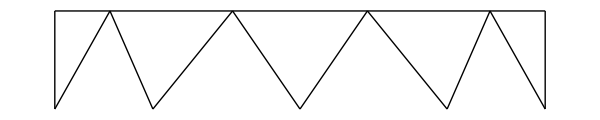

```mathematica
(* Illustration *)
graph={{{0,20},{100,20}}};
For[i=2,i≤Length[output[[4]]],i++,
graph=Append[graph,{{100*output[[7]][[i]],20},{100*output[[4]][[i]],0}}];
graph=Append[graph,{{100*output[[4]][[i]],0},{100*output[[8]][[i]],20}}]
]
Graphics[Line[graph],ImageSize->600]
```